# Math 350 - Lecture 14

Plotting functions and solution sets

## Types of plotting functions in two dimensions

There are many plotting functions in Mathematica. We have to choose the right tool for the job based on what we’re trying to visualize. The most important 2d plotting tools are Plot, ParametricPlot, ContourPlot, RegionPlot, and PolarPlot.

#### Plot

Plot is the most straightforward command, useful in situations where we are trying to graph functions of the form . For example, suppose we wanted a plot of .

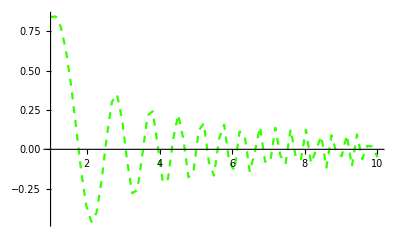

```mathematica
Plot[ Sin[x^2]/x, {x, 1, 10},PlotStyle->{Dashed,Hue[.3]},PlotPoints->2]
```

#### ParametricPlot

When we have a function given in terms of parametric equations  the appropriate command is ParametricPlot. Let us plot a parametric  function:

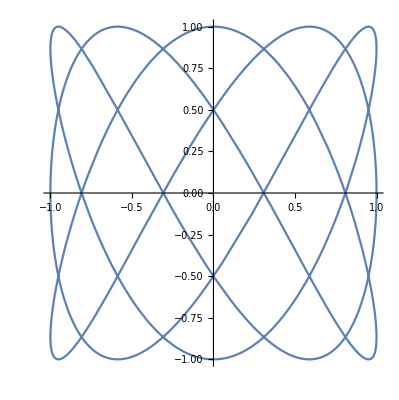

```mathematica
ParametricPlot[{Sin[3 t], Cos[5t]}, {t,0, 2Pi}]
```

#### ContourPlot

The function ContourPlot has many uses, but one of the most immediate is solving implicitly defined equations.

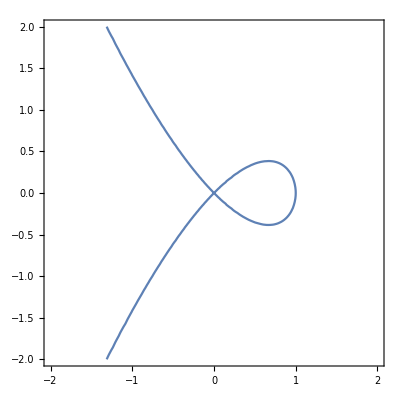

```mathematica
ContourPlot[x^3 - (x^2 - y^2) ==0, {x, -2, 2}, {y, -2, 2},Axes->True]
```

#### RegionPlot

Inequalities are best described graphically using the function RegionPlot.

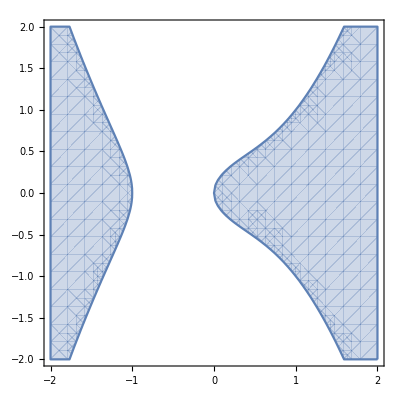

```mathematica
RegionPlot[x^4 + (x - 2y^2)>= 0, {x, -2, 2}, {y, -2, 2}]
```

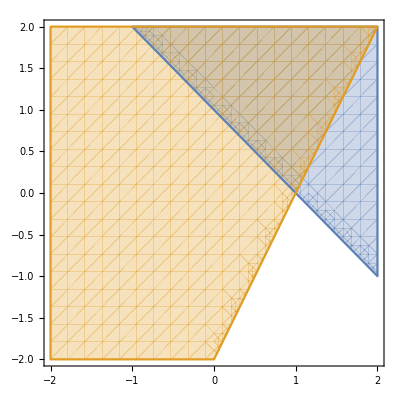

```mathematica
RegionPlot[{x+y >=1, 2x - y <= 2}, {x,-2,2},{y,-2,2}]
```

#### PolarPlot

To handle functions that map angles to radii in polar coordinates, we use PolarPlot.

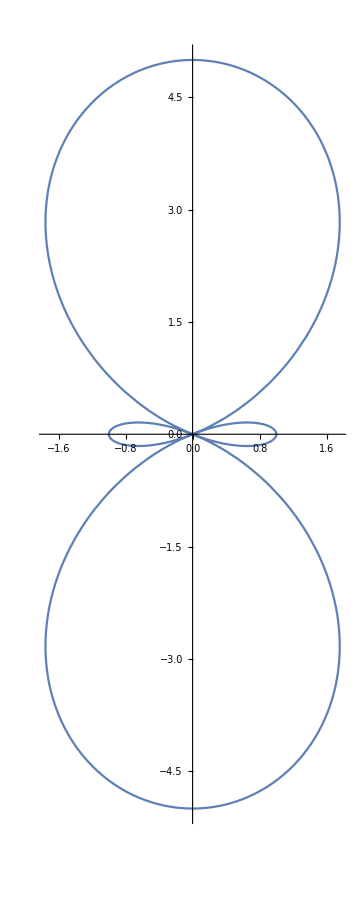

```mathematica
PolarPlot[2 - 3 Cos[2 t], {t, 0, 2 Pi}]
```

## Multiple plots

There are several ways of handling multiple plots in Mathematica - my preferred method is to generate individual plots, store them, and then plot them together using the command Show.

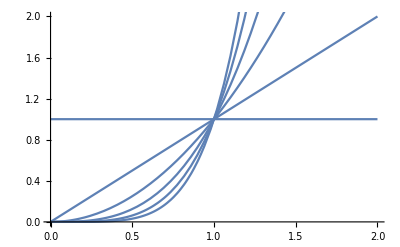

```mathematica
Show[Table[ Plot[x^i, {x, 0, 2}], {i, 0, 5}]]
```

If we need color to distinguish between plots, we can add that into the Table.

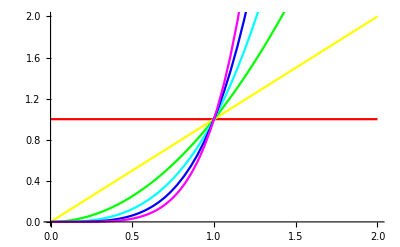

```mathematica
Show[Table[ Plot[x^i, {x, 0, 2}, PlotStyle->Hue[i/6]], {i, 0, 5}]]
```

```mathematica
p1 = Plot[x^2, {x, -1, 2}];
```

```mathematica
p2 = Plot[x^3, {x, -1, 2}];
```

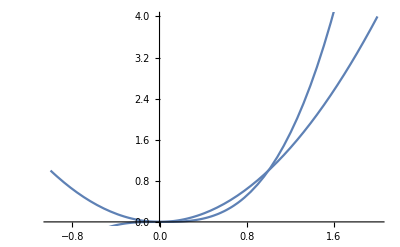

```mathematica
Show[p1,p2]
```

Another approach is to include all of the functions of interest into a single Plot command.

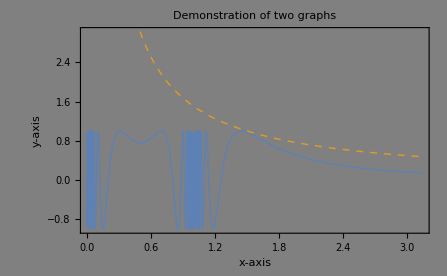

```mathematica
Plot[{Sin[1/(x^2-x)],1.5/x},{x,0,Pi},Frame->True,FrameStyle->Thick,FrameLabel->{x-axis,y-axis},PlotStyle->{{Thick},{Thick,Dashed}},Background->Gray,PlotLabel->"Demonstration of two graphs"]
```

## Types of plotting functions in three dimensions

We’re just going to be able to scratch the surface of 3D plots and the power that Mathematica has here, but the same basic operations are available as in the 2D case.

#### Plot3D

If we’re dealing with a function of the form , then we can plot with Plot3D.

```mathematica
Plot3D[Sqrt[3 - 2x^2 - 3y^2], {x, -2, 2}, {y, -2,2}]
```

-Graphics3D-

An important consideration in many functions is the number of sample points Mathematica uses to construct the surface.

```mathematica
Plot3D[x y Sin[x^2] Cos[y^2], {x, -2 Pi, 0}, {y, -2 Pi, 0}, PlotPoints->5]
```

-Graphics3D-

More points gives a better image, but takes longer to run.

```mathematica
Plot3D[x y Sin[x^2] Cos[y^2], {x, -2 Pi, 0}, {y, -2 Pi, 0}, PlotPoints->500]
```

-Graphics3D-

#### ContourPlot3D

Implicitly defined surfaces are again dealt with by using ContourPlot3D.

```mathematica
ContourPlot3D[x^4+y^4+z^4-(x^2+y^2+z^2)^2+3 (x^2+y^2+z^2)==3,{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-

## Complex functions

Mathematica has a nice set of built in tools for dealing with complex functions as well.

One of the most difficult things about complex functions is how hard they are to “see”.

```mathematica
ComplexPlot[z^2, {z, -1-I, 1+I}]
```

-Graphics-

```mathematica
ComplexPlot[1/z^2, {z, -1-I, 1+I}, PlotPoints->500]
```

-Graphics-

```mathematica
ComplexPlot3D[z^2, {z, -1-I, 1+I}]
```

-Graphics3D-

```mathematica
ComplexPlot3D[1/z^2, {z, -1-I, 1+I}]
```

-Graphics3D-

If you’re interested in what is going on here, check out https://reference.wolfram.com/language/guide/ComplexVisualization.html